## Import and process initial photometry

```mathematica
ClearAll["Global`*"]
ad:="C:\\ADDRESSGOESHERE\\"
SetDirectory[ad];
nm=FileNames[];
a:=Number
opt:={PlotStyle->Automatic,GridLines->Automatic,Filling->Bottom}
SetOptions[ListPlot,opt];
SetOptions[ListPolarPlot,opt]//Quiet;
plr:=0.7
opt2:={PlotRange->{{0,Automatic},{-plr,plr}},PlotTheme->"Grid",GridLines->None}
SetOptions[ListPolarPlot,opt2];
nm//MatrixForm
```

SetOptions::optnf: Filling is not a known option for ListPolarPlot.

(Initial_photometry.txt
Medium Atan2.csv
Medium.csv
Medium.jpg
Narrow Atan2.csv
Narrow.csv
Narrow.jpg
Narrow_Medium_and_Wide_Targets
oakoptimization.mph
SegmentedGeometryOptimization_v2.mph
StaticSegmentedGeometry_v2.mph)

```mathematica
n:=1
cut:=tmp1//Length
upl:=10^6
lwl:=0
lim:=1
raw=ReadList[ad<>nm[[n]],{a,String}];
tmp1=SortBy[raw,#[[2]]&];
tmp2=Delete[tmp1,Table[{k},{k,cut,tmp1//Length}]];
tmp3:=SortBy[Table[
{tmp2[[k,1]],tmp2[[k,2]]//ToExpression},
{k,1,tmp2//Length}],
#[[1]]&]
dat=Select[Select[Select[Select[
tmp3,
# [[2]]≤upl&],
# [[2]]≥lwl&],
#[[1]]<lim&],
#[[1]]>-lim&];
GraphicsRow[{dat//ListPolarPlot,dat//ListPlot},Dividers->All,ImageSize->Full]
```

-Graphics-

## Import target distribution example

```mathematica
targetdir:="C:\\ADDRESSGOESHERE\\";
SetDirectory[targetdir];
nm=FileNames[];
nm //MatrixForm
reflectortype = "Medium"; (*Possible types: "Narrow", "Medium", "Wide"*)
targetn = Position[StringContainsQ[nm,reflectortype],True];
targetnm = nm[[targetn[[1]]]]
target = Import[targetdir<>targetnm];
GraphicsRow[{target//ListPolarPlot,target//ListPlot},Dividers->All,ImageSize->Full]
```

(Initial Geometry.txt
Medium Target 2 Atan2.csv
Medium Target 2.csv
Medium Target 2.jpg
Narrow Target 1 Atan2.csv
Narrow Target 1.csv
Narrow Target 1.jpg
Wide Target 3 Atan2.csv
Wide Target 3.csv
Wide Target 3.jpg)

{Medium Target 2 Atan2.csv}

-Graphics-

## Moving average

```mathematica
win:=30
av[k_]:=MovingAverage[dat,k]
val:={1,win}
SetOptions[ListPolarPlot,ImageSize->Large];
ListPolarPlot[Table[av[k],{k,val}],PlotLegends->val]
```

-Graphics-

## Apply filter to initial photometry

```mathematica
inp=win//av;
ref=Nothing;
x[k_]:=inp[[k,1]]
(*Limits for argument manipulation*)
limAug := 4
limDmp := 4
limShf := 4
limElse := 4
```

```mathematica
fltrExp1[aug_,dmp_,shf_, element_]:=aug*
Exp[-dmp*(element-shf)^2]
fltrExp2[aug2_,dmp2_,shf_, element_]:=aug2*Exp[
-dmp2*(element+shf)^2]
fltrExp3[aug_,dmp_,shf2_, element_]:=aug*Exp[
-dmp*(element-shf2)^2]
fltrExp4[aug2_,dmp2_,shf2_, element_]:=aug2*Exp[
-dmp2*(element+shf2)^2]
fltrExp5[aug3_,dmp3_, element_]:=aug3*Exp[
-dmp3*element^2]
fltrCos[A_,f1_, element_]:=A*Abs[
Cos[f1*element]]
fltrSin1[B_,f2_, element_]:=B*Abs[
Sin[f2*element]]
fltrSin2[B1_,f3_, element_]:=B1*
Sin[f3*element]

fsum[aug_, aug2_, aug3_, dmp_, dmp2_,dmp3_, shf_, shf2_, A_, B_, B1_, f1_, f2_, f3_]:=Table[
{x[k],inp[[k,2]]+fltrExp1[aug,dmp,shf,x[k]]+
fltrExp2[aug2,dmp2,shf, x[k]]+fltrExp3[aug,dmp,shf2, x[k]]+
fltrExp4[aug2,dmp2,shf2, x[k]]+fltrExp5[aug3,dmp3, x[k]]+
fltrCos[A,f1, x[k]]+fltrSin1[B,f2, x[k]]+fltrSin2[B1,f3, x[k]]},
{k,1,inp//Length}];

Manipulate[
{ListPolarPlot[
fsum[aug, aug2, aug3, dmp, dmp2,dmp3, shf, shf2, A, B, B1, f1, f2, f3],
PlotRange->Automatic],
{aug, aug2, aug3, dmp, dmp2,dmp3, shf, shf2, A, B, B1, f1, f2, f3}},
{aug,0,limAug}, {aug2,0,limAug},{aug3,0,limAug},
{dmp,0,limDmp},{dmp2,0,limDmp},{dmp3,0,limDmp},
{shf,-limShf,limShf},{shf2,-limShf,limShf},
{A,0,limElse},{B,0,limElse},{B1,0,limElse},
{f1,0,limElse},{f2,0,limElse},{f3,0,limElse}
]
```

ListPolarPlot::lpn: fsum[2.69,1.335,1.345,3.395,2.595,2.885,-4,-4,0,0,0.,0,0,0.31] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPolarPlot::lpn will be suppressed during this calculation.

ListPolarPlot::lpn: fsum[2.69,1.335,1.345,3.395,2.595,2.885,-4,-4,0,0,0.,0,0,0.31] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPolarPlot::lpn will be suppressed during this calculation.

ListPolarPlot::lpn: fsum[2.69,1.335,1.345,3.395,2.595,2.885,-4,-4,0,0,0.,0,0,0.31] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPolarPlot::lpn will be suppressed during this calculation.

-Graphics-

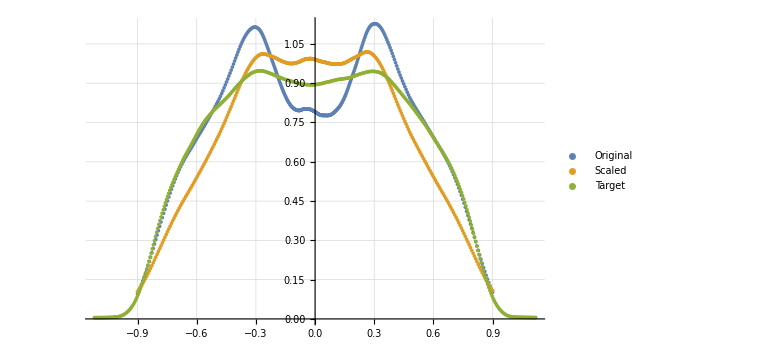

```mathematica
(*Insert best values as flt[] argument (no curly brackets)*)
flt = fsum[2.69,1.335,1.345,3.395,2.595,2.8850000000000002,-4,-4,0,0,0.,0,0,0.31];

S[x_]:=Sum[x[[k,2]],{k,1,x//Length}]
S0=S[dat];
α=S[flt]/S0;

bound:=2(*less value, narrower values close to zero*)
scaled=Table[{flt[[k,1]],flt[[k,2]]*UnitBox[flt[[k,1]]/bound]/α},{k,1,flt//Length}];

lg:={"Original","Scaled", "Target"}
ListPolarPlot[{inp,scaled, target},PlotLegends->lg]
ListPlot[{inp,scaled,target},PlotLegends->lg,Filling->None,ImageSize->Large]
```

```mathematica
rd:=6
L:=1.14
tf:=3.35*10^-8
tg=Table[{
0,
rd*Sin[scaled[[k,1]]],
rd*Cos[scaled[[k,1]]],
tf,
scaled[[k,2]]
},
{k,1,scaled//Length}];
```

```mathematica
(*ex[1]=scaled//ListPolarPlot;
targ:=ad<>reflectortype
Export[targ<>".csv",tg];
Export[targ<>" Atan2.csv",flt];
Export[targ<>".jpg",ex[1],ImageResolution->400];
SystemOpen[ad]*)
```